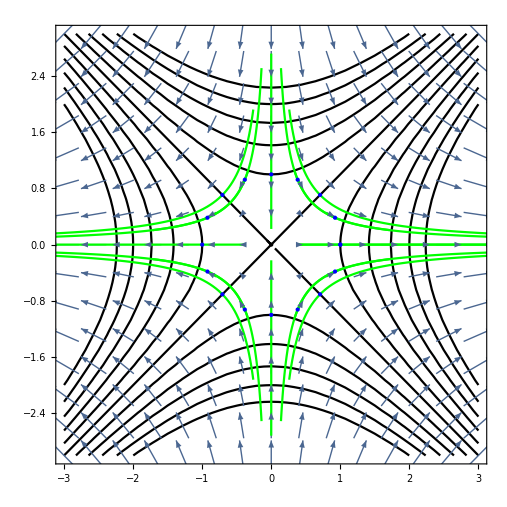

```mathematica
ClearAll["Global`*"]
levelsets=Show[Table[ContourPlot[x^2-y^2==z,{x,-3,3},{y,-3,3},ContourStyle->Black],{z,-5,5}],Graphics[Point[{0,0}]]];
gradient=VectorPlot[{2x,-2y},{x,-3,3},{y,-3,3}];

f[{x_,y_}]:=x^2-y^2;
(* gradient of f: R^2 -> R^2 *)
g[{a_,b_}]:=Grad[f[{x,y}],{x,y}]/.{x->a,y->b};
(* gamma at point {x,y}: R -> R^2 *)
gamma[{x_,y_}]:=Module[
{p},
p[t_]:=Evaluate@Array[Unique[][t]&,2];
Flatten[p[t]/.(DSolve[{p[0]=={x,y},p'[t]==g[p[t]]},p[t],t])]
];

flows=Show[Table[ParametricPlot[gamma[{Cos[theta],Sin[theta]}]/.t->i,{i,-0.5,0.75},PlotStyle->Green],{theta,0,2*Pi,Pi/8}]];
flowpoints=Graphics[{PointSize[Large],Blue,Point[Table[{Cos[theta],Sin[theta]},{theta,0,2*Pi,Pi/8}]]}];

output=Show[levelsets,gradient,flows,flowpoints]
```

```mathematica
Export["/Users/Henry/Downloads/flows2.jpg",output]
```

/Users/Henry/Downloads/flows2.jpg

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["/Users/Henry/Downloads/flows2.jpg"]]]
```

```mathematica
Show[Plot3D[x^2+y^2,{x,-5,5},{y,-5,5},Mesh->None,PlotRange->{{-3,3},{-3,3},{0,5}},BoxRatios->{1, 1, 1},ClippingStyle->None]]
Export["/Users/Henry/Downloads/parabaloid.jpg",%]
(*Export["/Users/Henry/Downloads/hyperbaloid.jpg",Plot3D[x^2-y^2,{x,-5,5},{y,-5,5}]]*)
```

-Graphics3D-

/Users/Henry/Downloads/parabaloid.jpg